```mathematica
Clear["Global`*"]
```

定义矩阵

```mathematica
h=({{0, -2.97*(Exp[I*(Sqrt[3]*kx/2-ky/2)]+Exp[I*ky]+Exp[I*(-Sqrt[3]*kx/2-ky/2)]), 0, -0.33}, {-2.97*(Exp[-I*(Sqrt[3]*kx/2-ky/2)]+Exp[-I*ky]+Exp[-I*(-Sqrt[3]*kx/2-ky/2)]), 0, 0, 0}, {0, 0, 0, -2.97*(Exp[I*(Sqrt[3]*kx/2-ky/2)]+Exp[I*ky]+Exp[I*(-Sqrt[3]*kx/2-ky/2)])}, {-0.33, 0, -2.97*(Exp[-I*(Sqrt[3]*kx/2-ky/2)]+Exp[-I*ky]+Exp[-I*(-Sqrt[3]*kx/2-ky/2)]), 0}})
```

{{0,-2.97 (ⅇ^(ⅈ (-(√3 kx)/2-ky/2))+ⅇ^(ⅈ ((√3 kx)/2-ky/2))+ⅇ^(ⅈ ky)),0,-0.33},{-2.97 (ⅇ^(-ⅈ (-(√3 kx)/2-ky/2))+ⅇ^(-ⅈ ((√3 kx)/2-ky/2))+ⅇ^(-ⅈ ky)),0,0,0},{0,0,0,-2.97 (ⅇ^(ⅈ (-(√3 kx)/2-ky/2))+ⅇ^(ⅈ ((√3 kx)/2-ky/2))+ⅇ^(ⅈ ky))},{-0.33,0,-2.97 (ⅇ^(-ⅈ (-(√3 kx)/2-ky/2))+ⅇ^(-ⅈ ((√3 kx)/2-ky/2))+ⅇ^(-ⅈ ky)),0}}

定义求本征值的函数

```mathematica
eig[kx_,ky_]:=h//Eigenvalues//ToRadicals//Evaluate
```

将它编译（真的快很多，快10倍起步）

```mathematica
comeig=Compile[{{kx,_Real},{ky,_Real}},eig[kx,ky]//Evaluate]
```

CompiledFunction[…]

```mathematica
list=Table[Re[comeig[kx,ky]],{kx,-Pi,Pi,0.1},{ky,-Pi,Pi,0.1}]
```

{{{-6.34899,6.34899,-6.01899,6.01899},61,{6.66497,-6.66497,6.33497,-6.33497}},61,{{-6.18419,3},62}}
 |  |  |  |

```mathematica
sortedlist=Map[Sort[#]&,list,{-2}]
```

{{{-6.34899,-6.01899,6.01899,6.34899},61,{-6.66497,-6.33497,6.33497,6.66497}},61,{{-6.18419,3},62}}
 |  |  |  |

```mathematica
sortedlist[[All,All,1]]//ListPlot3D
```

-Graphics3D-

下面是不排序的情况，有褶皱

```mathematica
Table[Abs[eig[kx,ky]],{kx,-Pi,Pi,0.1},{ky,-Pi,Pi,0.1}]
```

{{{6.34899,6.34899,6.01899,6.01899},61,{6.66497,6.66497,6.33497,6.33497}},61,{1}}
 |  |  |  |

```mathematica
Table[Plot3D[Re[comeig[kx,ky]][[i]],{kx,-Pi,Pi},{ky,-Pi,Pi},PerformanceGoal->"Quality",PlotRange->Full],{i,1,4}]
```

{-Graphics3D-,-Graphics3D-,-Graphics3D-,-Graphics3D-}

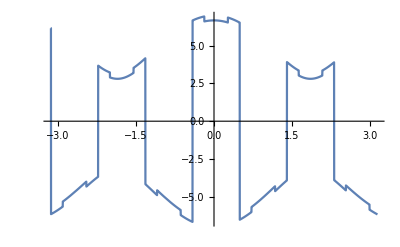
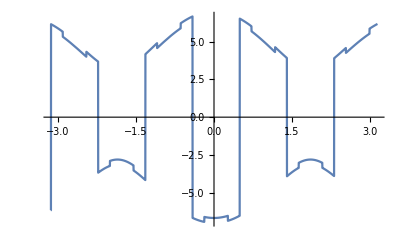

```mathematica
Table[Plot[Re[comeig[kx,1]][[i]],{kx,-Pi,Pi},PerformanceGoal->"Quality",PlotRange->Full],{i,1,2}]
```

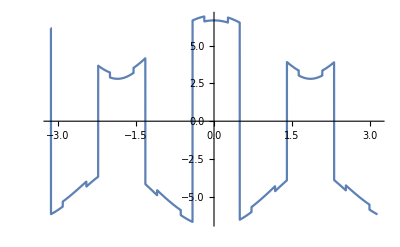

```mathematica
Plot[Re@comeig[kx,1][[1]],{kx,-Pi,Pi},PlotPoints->100]
```

```mathematica
Re@eig[kx,ky][[1]]
```

-0.5 Re[ⅇ^(-2 ⅈ √3 kx-3 ⅈ ky) √(35.2836 (1. ⅇ^(7/2 ⅈ √3 kx+(9 ⅈ ky)/2)+1. ⅇ^(9/2 ⅈ √3 kx+(9 ⅈ ky)/2)+1. ⅇ^(3 ⅈ √3 kx+6 ⅈ ky)+3.00617 ⅇ^(4 ⅈ √3 kx+6 ⅈ ky)+1. ⅇ^(5 ⅈ √3 kx+6 ⅈ ky)+1. ⅇ^(7/2 ⅈ √3 kx+(15 ⅈ ky)/2)+1. ⅇ^(9/2 ⅈ √3 kx+(15 ⅈ ky)/2))-2 √(311.233 (1. ⅇ^(7/2 ⅈ √3 kx+(9 ⅈ ky)/2)+1. ⅇ^(9/2 ⅈ √3 kx+(9 ⅈ ky)/2)+1. ⅇ^(3 ⅈ √3 kx+6 ⅈ ky)+3.00617 ⅇ^(4 ⅈ √3 kx+6 ⅈ ky)+1. ⅇ^(5 ⅈ √3 kx+6 ⅈ ky)+1. ⅇ^(7/2 ⅈ √3 kx+(15 ⅈ ky)/2)+1. ⅇ^(9/2 ⅈ √3 kx+(15 ⅈ ky)/2))^2-311.233 (1. ⅇ^(7 ⅈ √3 kx+9 ⅈ ky)+2. ⅇ^(8 ⅈ √3 kx+9 ⅈ ky)+1. ⅇ^(9 ⅈ √3 kx+9 ⅈ ky)+2. ⅇ^(13/2 ⅈ √3 kx+(21 ⅈ ky)/2)+8. ⅇ^(15/2 ⅈ √3 kx+(21 ⅈ ky)/2)+8. ⅇ^(17/2 ⅈ √3 kx+(21 ⅈ ky)/2)+2. ⅇ^(19/2 ⅈ √3 kx+(21 ⅈ ky)/2)+1. ⅇ^(6 ⅈ √3 kx+12 ⅈ ky)+8. ⅇ^(7 ⅈ √3 kx+12 ⅈ ky)+15. ⅇ^(8 ⅈ √3 kx+12 ⅈ ky)+8. ⅇ^(9 ⅈ √3 kx+12 ⅈ ky)+1. ⅇ^(10 ⅈ √3 kx+12 ⅈ ky)+2. ⅇ^(13/2 ⅈ √3 kx+(27 ⅈ ky)/2)+8. ⅇ^(15/2 ⅈ √3 kx+(27 ⅈ ky)/2)+8. ⅇ^(17/2 ⅈ √3 kx+(27 ⅈ ky)/2)+2. ⅇ^(19/2 ⅈ √3 kx+(27 ⅈ ky)/2)+1. ⅇ^(7 ⅈ √3 kx+15 ⅈ ky)+2. ⅇ^(8 ⅈ √3 kx+15 ⅈ ky)+1. ⅇ^(9 ⅈ √3 kx+15 ⅈ ky))))]

```mathematica
D[Re@eig[kx,1][[1]],{kx}]/.{kx->0.49}
```

(-1.87324-9.9476×10^-14 ⅈ) Re'[-13.0461-4.4964×10^-15 ⅈ]